# Archived code (mask processing to regions)

```mathematica
(* -Graphics3D-*)
```

### pseudo-axis of symmetry

```mathematica
(*
Clear@findSym;
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; 
(* we subtract from each point the center of mass. This gives us a vector of n number of points the {x,y} coordinates of which are
displacements from the centroids. We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of
two coordinates which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)

(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]];
{centerOfMass,v1,v2}
]
*)
```

```mathematica
(*
Clear@bisectRegion;
bisectRegion[mask_,option_:True]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp={},pt1,pt2,
list,trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask},
{centerofMass,v1,v2}=findSym[mask];
ℛ1=ImageMesh[mask];
pixelordered=MeshPrimitives[ℛ1,0]/.Point[x_]:> x;
ℛ2=InfiniteLine[{centerofMass,centerofMass+v2}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[option,temp=Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]]];

npixelordered = N@pixelordered;

nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];

Join[{temp},{centerofMass},pt1,pt2]
]
*)
```

### rotate mask and align with coordinates

```mathematica
(*
Clear@rotateMask;
rotateMask[mask_?ImageQ]:= Module[{temp,centroid,pts1,pts2,grad,
perimeterpts,norm,θ,rotateFn,canvas,rotatedpts,dim = ImageDimensions@mask,translationFn,transpts},
{temp,centroid,pts1,pts2}=bisectRegion[mask];
perimeterpts= PixelValuePositions[MorphologicalPerimeter@mask,1];
norm = Normalize[Subtract[pts2,pts1]];
θ=VectorAngle[norm,{0,1}](180/π);
grad=(pts2[[2]]-pts1[[2]])/(pts2[[1]]-pts1[[1]]);
θ=Which[grad>0,If[θ>90,-θ,θ],grad<0,If[θ<90,-θ,θ]];
rotateFn=RotationTransform[θ Degree,norm];
canvas=ConstantImage[0,dim];
rotatedpts=rotateFn[perimeterpts~Append~centroid];
translationFn = TranslationTransform[dim/2-Last@rotatedpts];
transpts= Abs[translationFn@Most@rotatedpts];
ReplacePixelValue[canvas,transpts-> 1]//FillingTransform
];
*)
```

### extract equivalent radius from mesh

```mathematica
(*
Clear@extractRadii;
extractRadii[mask_?ImageQ]:=Block[{mesh,centroid,mesh2Dpts,
rotateTransform,mesh3Dpts,hullmesh,r},
mesh=ImageMesh[mask];
centroid= Append[RegionCentroid[mesh],0];
mesh2Dpts=MeshPrimitives[mesh,0]/.Point[x_]:> x;rotateTransform=RotationTransform[3.Degree,{0,1,0},centroid];mesh3Dpts=NestList[rotateTransform,ArrayFlatten[{{mesh2Dpts,0}}],59];
hullmesh=ConvexHullMesh[Flatten[mesh3Dpts,1]];
Print[mask,BoundaryMeshRegion[hullmesh,ImageSize->Tiny,Boxed->True]];
Values@(First@@Solve[4/3Pi r^3 ==Volume[hullmesh],r∈Reals])
];
*)
```

```mathematica
(*
Fn[arg_]:=With[{pixelsize=0.633},
MapThread[{#1, First@*Values@ComponentMeasurements[MorphologicalComponents@#2,"EquivalentDiskRadius"]*pixelsize}&,arg]
];
*)
```

```mathematica
(*
getRadius[directory_]:=With[{pixelsize=0.633},
Module[{files,filteredfiles,timestamps,masks,deformedmaskpos,deformedmasks,rotatedmasks,maskseries1,maskseries2,timestamps1,timestamps2,aggregate1R,aggregate2R,repmasks},
files=Import[directory];
filteredfiles=Flatten@StringCases[files,__~~"Mask.tif"];timestamps=Flatten[StringCases[filteredfiles,x:__ ~~" hours"~~___ :> ToExpression@x]];masks=Import[directory<>#]&/@(filteredfiles);deformedmaskpos=Position[timestamps,_?(#>72&)];deformedmasks=Extract[masks,deformedmaskpos];
Which[
deformedmaskpos≠ {},
(rotatedmasks=rotateMask/@deformedmasks;
repmasks=ReplacePart[masks,Thread[deformedmaskpos-> rotatedmasks]];
{maskseries1,timestamps1}=Take[#,Min@deformedmaskpos-1]&/@{repmasks,timestamps};
{maskseries2,timestamps2} = Drop[#,Min@deformedmaskpos-1]&/@{repmasks,timestamps};
aggregate1R=Fn[{timestamps1,maskseries1}];
aggregate2R=Thread[{timestamps2,Composition[Times[#,pixelsize]&,extractRadii]/@rotatedmasks}];
aggregate1R~Join~aggregate2R),
True,
Fn[{timestamps,masks}]
]
]
];
*)
```

```mathematica
(*
getRadius["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@radius-cellcount vs time\\chi pos\\aggregate 6 raw images\\"] (* works with code archived in the notebook *) 
*)
```

# Volume of aggregates

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\growth-evolution\\masktoRegion3D.wl";
```

```mathematica
equivalentRadii["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@radius-cellcount vs time\\chi pos\\aggregate 7 raw images\\"]
```

-Graphics--Graphics3D-

-Graphics--Graphics3D-

-Graphics--Graphics3D-

«3 more identical outputs»

{{48,40.553},{53,43.3279},{56,43.5145},{60,47.6514},{63,49.3734},{65,51.8088},{68,56.1129},{72,60.642},{76,67.7028},{80,71.2092},{82,74.4753},{85,77.9488},{89,84.562},{92,90.6945}}

# Load results

```mathematica
(* radius vs time for Chi +ve and Chi -ve cases *)
```

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\analysis notebooks\\growth-evolution\\Vol_gastruloid.mx"];
```

```mathematica
(* volume of aggregate (+ve chiron) *)
```

```mathematica
volChi = DeleteCases[MapAt[4/3*Pi*(#*10^-3)^3&,aggregateChiR,{All,All,2}],{24,_},{2}];
```

```mathematica
(* volume of aggregate (-ve chiron) *)
```

```mathematica
volMinChi = DeleteCases[MapAt[4/3*Pi*(# *10^-3)^3&,aggregateChiNegR,{All,All,2}],{24,_},{2}];
```

# Analysis

## volume plots

### Chi +ve

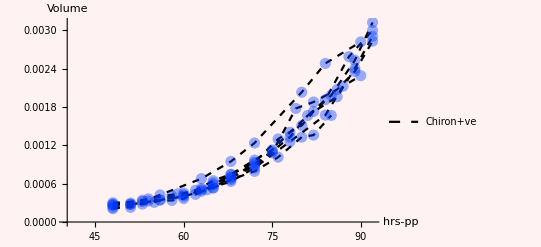

```mathematica
chiPlot=Show[
ListPlot[#1,Joined->True,PlotStyle->{{Dashed,Thin,Black}},PlotRange->{{40,All},Automatic},
PlotLegends->{#2}],
ListPlot[#1,PlotStyle->{{XYZColor[0,0,1,0.4],PointSize[0.02]}}],
AxesLabel->(Style[#,{GrayLevel[0.5],Bold,FontFamily->"Consolas",FontSize->16}]&/@{"hrs-pp",#3}),
AxesStyle->Directive[Black,Bold, 12],
Background-> Lighter@LightPink
]&[Most@volChi,"Chiron+ve","Volume"]
```

### Chi -ve

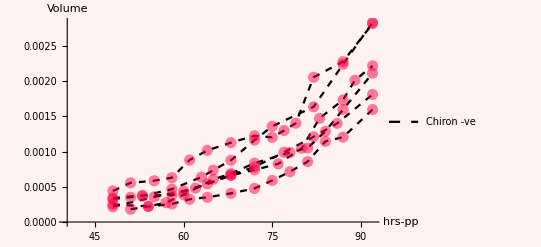

```mathematica
chiNegPlot=Show[
ListPlot[#1,Joined->True,PlotStyle->{{Dashed,Thin,Black}},PlotRange->{{40,All},Automatic},
PlotLegends->{#2}],
ListPlot[#1,PlotStyle->{{XYZColor[1,0,0,0.5],PointSize[0.02]}}],
AxesLabel->(Style[#,{GrayLevel[0.4],Bold,FontFamily->"Consolas",FontSize->16}]&/@{"hrs-pp",#3}),
AxesStyle->Directive[Black,Bold, 12],
Background-> Lighter@LightPink]&[volMinChi,"Chiron -ve","Volume"]
```

### combined

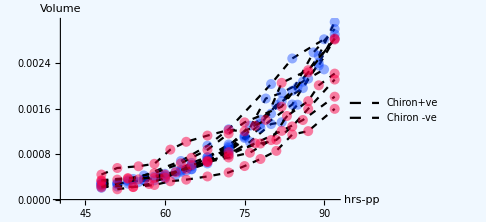

```mathematica
Show[chiPlot,chiNegPlot,Background->Nest[Lighter,LightBlue,2],ImageSize->Medium]
```

## volume plot (Log)

```mathematica
linevolChi=Table[{x,Exp[a x + b]} /.# ,{x,45,95}]&[FindFit[MapAt[Log,Flatten[Most@volChi,1],{All,2}],a x + b, {a,b},x]];
```

```mathematica
linevolMinChi=Table[{x,Exp[a x + b]} /.# ,{x,45,95}]&[FindFit[MapAt[Log,Flatten[volMinChi,1],{All,2}],a x + b, {a,b},x]];
```

```mathematica
plot=Show[
ListLogPlot[linevolChi,Joined->True,PlotStyle->{Dashed,Thick,Black}],
ListLogPlot[linevolMinChi,Joined->True,PlotStyle->{Dashed,Thick,Gray}],
ListLogPlot[Flatten[Most@volChi,1],PlotStyle->{RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],PointSize[0.02]},PlotLegends->  {"Chiron +ve"}],
ListLogPlot[Flatten[volMinChi,1],PlotStyle->{RGBColor[0.8772074195392446, 0.34739015904351433, 0.3403844448018665],PointSize[0.02]},PlotLegends->  {"Chiron -ve"}],
AxesStyle-> {{Bold,FontSize-> 14},{Bold,FontSize-> 14}},AxesLabel-> (Style[#,Bold,Black]&/@{"hrs post-plating","Volume ( mm^3)"}),
PlotRange-> All,ImageSize->Large,Background-> None
]//Rasterize[#,"Image",ImageResolution->500]&
```

-Graphics-

#### binned version

```mathematica
chibins=Flatten[BinLists[Flatten[Most@volChi,1],5,1],1];
barschibins=Map[N@*StandardDeviation]@chibins;
binnedchi = Map[N@*Mean]@chibins;
chibinsLinFit=Table[{x,Exp[a x + b]} /.# ,{x,45,95}]&[FindFit[MapAt[Log,binnedchi,{All,2}],a x + b, {a,b},x]];
```

```mathematica
chiMinbins=Flatten[BinLists[Flatten[volMinChi,1],5,1],1];
barschiMinbins=Map[N@*StandardDeviation]@chiMinbins;
binnedChiMins=Map[N@*Mean]@chiMinbins;
chiMinbinsLinFit=Table[{x,Exp[a x + b]} /.# ,{x,45,95}]&[FindFit[MapAt[Log,binnedChiMins,{All,2}],a x + b, {a,b},x]];
```

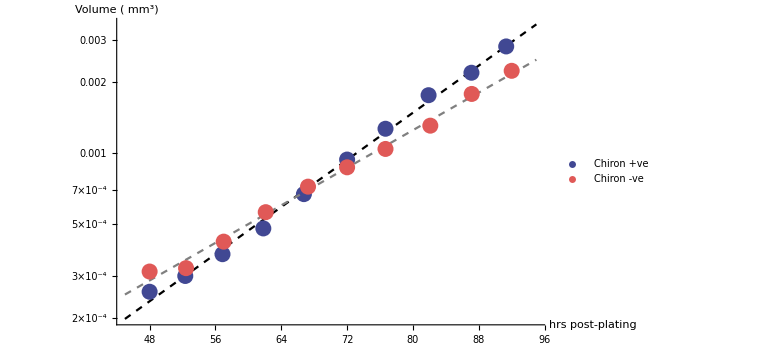

```mathematica
Show[
ListLogPlot[chibinsLinFit,Joined->True,PlotStyle->{Dashed,Thick,Black}],
ListLogPlot[binnedchi,PlotStyle->{RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],PointSize[0.02]},PlotLegends->  {"Chiron +ve"}],
ListLogPlot[chiMinbinsLinFit,Joined->True,PlotStyle->{Dashed,Thick,Gray}],
ListLogPlot[binnedChiMins,PlotStyle->{RGBColor[0.8772074195392446, 0.34739015904351433, 0.3403844448018665],PointSize[0.02]},
PlotLegends->  {"Chiron -ve"}],AxesStyle-> Bold,AxesLabel-> {"hrs post-plating","Volume ( mm^3)"},
PlotRange-> All,ImageSize->Large
]
```

### doubling time

```mathematica
ClearAll[gradientLogFit,a,b];
gradientLogFit[data_]:= Module[{time,logvol,valsChi,grad,intercept,doublingt},
{time,logvol}=Transpose[data]/.{p:{__},x:{__}}:> {p,N@Log[x]};
valsChi=SortBy[Thread[{time,logvol}],First];
{grad,intercept}={a,b}/.FindFit[valsChi,a x +b,{a,b},x];
grad
]
```

```mathematica
gradChi=(#/Log[2.])&@*gradientLogFit/@Most[volChi];
```

```mathematica
gradControl=(#/Log[2.])&@*gradientLogFit/@volMinChi;
```

```mathematica
BoxWhiskerChart[{gradChi,gradControl},{{"Whiskers", Thick}, {"Fences", Thick}},ChartStyle->{RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],RGBColor[0.8772074195392446, 0.34739015904351433, 0.3403844448018665]},
ChartLabels->{"Chiron +ve","Control"},
PlotLabel->Style["Growth Rate (hr^-1)",{Black,FontSize->16}],
FrameStyle->Thin,FrameTicksStyle->14,Background->None
]//Rasterize[#,"Image",ImageResolution->500]&
```

-Graphics-

```mathematica
Length/@{gradChi,gradControl}
```

{7,6}

```mathematica
Column@MannWhitneyTest[{gradChi,gradControl},0,{"TestDataTable","TestConclusion"}]
```

| Statistic | P-Value
Mann-Whitney | 42. | 0.00340524
The null hypothesis that the median difference is 0 is rejected at the 5 percent level based on the Mann-Whitney test.

```mathematica
Print[Style["Growth Rate (Control): ",RGBColor[0.8772074195392446, 0.34739015904351433, 0.3403844448018665],Bold,FontSize-> 18], Style[ToString[(Mean@gradControl)^-1]<>" hr",FontSize->18]]
```

Growth Rate (Control): 14.4041 hr

```mathematica
Print[Style["Growth Rate (Chi +ve): ",RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],Bold,FontSize-> 18], Style[ToString[(Mean@gradChi)^-1]<>" hr",FontSize->18]]
```

Growth Rate (Chi +ve): 11.9365 hr